QED cascades induced by circularly polarized laser fields

N. V. Elkina,A. M. Fedotov, I. Yu. Kostyukov, M. V. Legkov, N. B. Narozhny, E. N. Nerush, and H. Ruhl, PHYSICAL REVIEW SPECIAL TOPICS - ACCELERATORS AND BEAMS 14, 054401 (2011)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

```mathematica
(* Airy function *)
Clear[ξ,x]
Refine[((1/π Integrate[Cos[ξ^3/3+ξ x],{ξ,0,∞}]//Normal)-AiryAi[x])//Simplify,{x>0}]
```

0

## Equations 7, 8, 9

```mathematica
Clear[p0,p0x,p0y,Ε,Εx,Εy,E0,ω,sols,a0,m,c,e,t0,px,py,eq,χe]

(* eq 6 Ε field components *)
Ε={E0 Cos[ω t],E0 Sin[ω t]};

(* eq 7 equation of motion *)
eq={D[px[t],t],D[py[t],t]}==e Ε;

(* eq 8 solution *)
sols=DSolve[{eq,{px[t0],py[t0]}=={p0x,p0y}},{px[t],py[t]},t]//Simplify;
E0 = m ω c a0/e;
sols=sols//FullSimplify;

(* t0=0 and initially at rest p0=0*)
px=sols[[1,1,2]]/.{t0->0,p0x->0}
py=sols[[1,2,2]]/.{t0->0,p0y->0}

(* get energy ϵe *)
ϵe=Refine[m c^2 Sqrt[(px/(m c))^2+(py/(m c))^2+1]//Simplify,{m>0,c>0}]//Simplify
(* check eq 9a *)
ϵe-m c^2 Sqrt[1+4 a0^2 Sin[(ω t)/2]^2]//Simplify

(* get energy χe *)
p={px,py};
χe=Refine[(e ℏ)/(m^3 c^4)Sqrt[Refine[(Norm[(ϵe Ε)/c]^2-(p.Ε)^2)//Simplify,{a0>0,m>0,c>0,e>0,ω>0,t>0}]//FullSimplify],{a0>0,m>0,c>0,e>0,ω>0,t>0}]

(* check eq 9b *)
χe-(e ℏ E0)/(m^2 c^3)Sqrt[1+4 a0^2 Sin[(ω t)/2]^4]//Simplify
```

a0 c m Sin[t ω]

a0 c m (1-Cos[t ω])

c^2 m √(1+2 a0^2-2 a0^2 Cos[t ω])

0

(7.42462×10^-35 a0 ω √(2+3 a0^2+a0^2 (-4 Cos[t ω]+Cos[2 t ω])))/(c^2 m)

-(1.06911×10^-50 a0 ω √(2+3 a0^2-4 a0^2 Cos[t ω]+a0^2 Cos[2 t ω]))/(c^2 m)

## Equations 10, 11

```mathematica
Clear[p0,p0x,p0y,Ε,Εx,Εy,E0,ω,sols,a0,m,c,e,t0,px,py,eq,χe,r1,r2,ES,ℏ]

(* eq 10a *)
r1=Refine[Asymptotic[m c^2 Sqrt[1+4 a0^2 Sin[(ω t)/2]^2],a0->∞],{a0>0,t>0,ω>0,Sin[(t ω)/2]>0}]
Series[r1,{t,0,1}]/.{a0->(e E0)/(m c ω)}

(* eq 10b *)
r2=Refine[Asymptotic[(e ℏ E0)/(m^2 c^3)Sqrt[1+4 a0^2 Sin[(ω t)/2]^4],a0->∞],{a0>0,t>0,ω>0,Sin[(t ω)/2]>0}]
(* check *)
r22=Series[r2 ,{t,0,2}]//.{a0->(e E0)/(m c ω)}//Normal
(r22-(1/2(E0/ES)^2(m c^2 ω)/ℏ t^2)//Simplify)/.{ℏ->(m^2 c^3)/(e ES)}

(* eq 11 t_acc: this is estimated without the √2 *)
tacc=Solve[(e^2 E0^2 t^2 ω ℏ)/(c^4 m^3)==1,t][[2,1,2]]
(* check. α μ will not depend on α *)
Refine[(ℏ/(α m c^2 μ)Sqrt[(m c^2)/(ℏ ω)]-tacc)//.{μ->E0/(α ES),ES->(m^2 c^3)/(e ℏ)}//Simplify,{m>0,c>0,ω>0,ℏ>0}]//Simplify
```

2 a0 c^2 m Sin[(t ω)/2]

c e E0 t+O[t]^2

(2 a0 e E0 ℏ Sin[(t ω)/2]^2)/(c^3 m^2)

(e^2 E0^2 t^2 ω ℏ)/(2 c^4 m^3)

0

(c^2 m^(3/2))/(e E0 √ω √ℏ)

0

## Figure 4 a

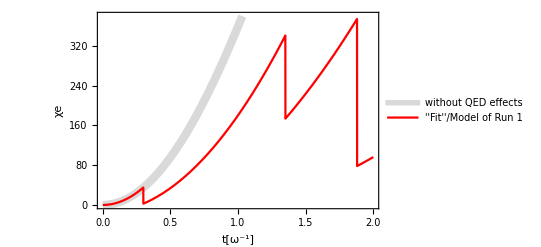

```mathematica
Clear[χe,e,ℏ,E0,m,c,a0,ω,t,ES,χet2]

χe=(e ℏ E0)/(m^2 c^3)Sqrt[1+4 a0^2 Sin[(ω t)/2]^4];
χet2=1/2(E0/ES)^2*(m c^2 ω)/ℏ t^2;(*10b*)
E0=(a0 m ω c)/e;

c=3 10^8;(*[m/s]*)
e=1.6 10^-19;(*[C]*)
ℏ=1.05 10^-34;(*[Js]*)
m=9.1 10^-31;(*[Kg]*)
ES=m^2 c^3/(e ℏ);(*[V/m]*)

ω=e/ℏ;(*[s], 1eV *)
a0=2 10^4;

(* the red curve is only an approximation of the simulation data of the paper *)
Plot[{χe/.{t->tω/ω},(χet2  HeavisideTheta[0.3-tω]+(0.5χet2-15)HeavisideTheta[tω-0.3]HeavisideTheta[1.35-tω]+(0.3χet2-40)HeavisideTheta[tω-1.35]HeavisideTheta[1.88-tω]+(0.1χet2-60)HeavisideTheta[tω-1.88]HeavisideTheta[3-tω])/.{t->tω/ω}},{tω,0,2},PlotRange->{0,380},PlotStyle->{{LightGray,Thickness[0.015]},Red,Default},Frame->True,FrameLabel->{"t[ω^-1]","χe"},PlotLegends->{"without QED effects","''Fit''/Model of Run 1"}]
```

## Figure 5

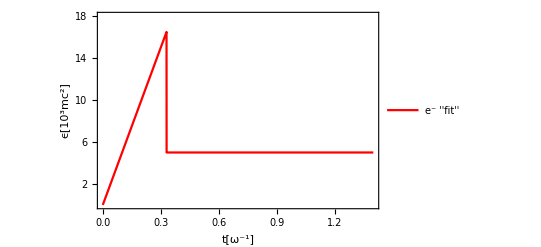

```mathematica
Clear[χe,e,ℏ,E0,m,c,a0,ω,t,ES,χet2]

χe=(e ℏ E0)/(m^2 c^3)Sqrt[1+4 a0^2 Sin[(ω t)/2]^4];
χet2=1/2(E0/ES)^2*(m c^2 ω)/ℏ t^2;(*10b*)
E0=(a0 m ω c)/e;

c=3 10^8;(*[m/s]*)
e=1.6 10^-19;(*[C]*)
ℏ=1.05 10^-34;(*[Js]*)
m=9.1 10^-31;(*[Kg]*)
ES=m^2 c^3/(e ℏ);(*[V/m]*)

ω=1 e/ℏ;(*[s], 1eV *)
a0=5 10^4;

(* the red curve is only an approximation of the simulation data of the paper *)
Plot[{((c e E0 t)/(10^3 m c^2)HeavisideTheta[0.33-tω]+5HeavisideTheta[tω-0.33])/.{t->tω/ω}},{tω,0,1.4},PlotRange->{0,18},PlotStyle->{Red,Default},Frame->True,FrameLabel->{"t[ω^-1]","ϵ[10^3mc^2]"},PlotLegends->{"e^- ''fit''"},FrameTicks->{Automatic,{2,4,6,8,10,12,14,16,18}}]
```

## Figure 7

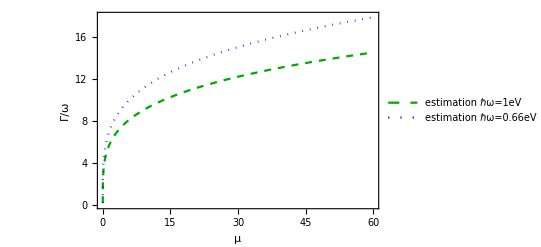

```mathematica
Clear[χe,e,ℏ,E0,m,c,a0,ω,t,ES,Γ,μ,α]

c=3 10^8;(*[m/s]*)
e=1.6 10^-19;(*[C]*)
ℏ=1.05 10^-34;(*[Js]*)
m=9.1 10^-31;(*[Kg]*)
ES=m^2 c^3/(e ℏ);(*[V/m]*)
α=1/137;(*[]*)

(* eq 13 *)
Γ=α μ^(1/4)Sqrt[(m c^2 ω)/ℏ];

Plot[{Γ/ω/.{ω->1 e/ℏ},Γ/ω/.{ω->0.66 e/ℏ}},{μ,0,60},PlotRange->{0,18},Frame->True,FrameLabel->{"μ","Γ/ω"},PlotStyle->{{Dashed,Darker[Green]},{Dotted,Blue}},PlotLegends->{"estimation ℏω=1eV","estimation ℏω=0.66eV"}]
```

## Appendix

```mathematica
Clear[x]
D[AiryAi[x],{x,2}]-x AiryAi[x]
-2/3 Integrate[x^3 AiryAi[x],{x,0,∞}]
```

0

-4/9